```mathematica
{x(x-1)x/Sqrt[x^2+y^2], -0.5*(4*(x^2+y^2)-3*Sqrt[x^2+y^2])*(-y/Sqrt[x^2+y^2])}
```

{((-1+x) x^2)/(√(x^2+y^2)),(0.5 y (-3 √(x^2+y^2)+4 (x^2+y^2)))/(√(x^2+y^2))}

```mathematica
VectorPlot[{x(x-1)x/Sqrt[x^2+y^2], -0.5*(4*(x^2+y^2)-3*Sqrt[x^2+y^2])*(-y/Sqrt[x^2+y^2])},{x,-1,1},{y,-1,1}]
```

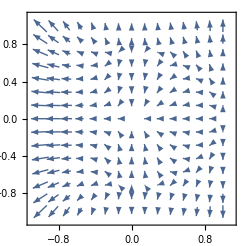

-Graphics-

Current field
Here we convert the initial conditions for the current (j) from polar coordinates to Cartesian using Mathematica’s routines. The current is taken from Gusakov’s notes (ubr.pdf).

```mathematica
j[x_,y_] = TransformedField["Polar"->"Cartesian",{r*(r-1)*Cos[θ],0.5*(4 r^2-3r)*(- Sin[θ])},{r,θ}->{x,y}]*HeavisideTheta[1-x^2-y^2] // Simplify
```

{(y^2 (2.-1.5/(√(x^2+y^2)))+x^2 (1-1/(√(x^2+y^2)))) HeavisideTheta[1-x^2-y^2],-(1. x y (-0.5+1. √(x^2+y^2)) HeavisideTheta[1-x^2-y^2])/(√(x^2+y^2))}

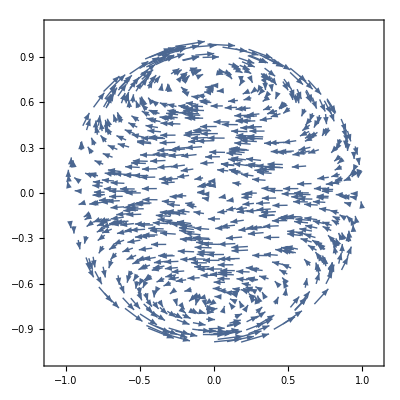

```mathematica
VectorPlot[j[x,y],{x,-1,1},{y,-1,1},VectorPoints->RandomReal[{-1,1},{1000,2}]]
```

```mathematica
We also want to confirm that Div of the field (taking into account cylindrical geometry) is zero.
```

```mathematica
Div[j[x,y]*2*pi*y,{x,y} ] // Simplify
```

pi x y^3 (4.-2./(√(x^2+y^2))) DiracDelta[-1+x^2+y^2]-4 pi x y (y^2 (2.-1.5/(√(x^2+y^2)))+x^2 (1-1/(√(x^2+y^2)))) DiracDelta[-1+x^2+y^2]+(pi x y (4.44089×10^-16 x^4+8.88178×10^-16 x^2 y^2+2.22045×10^-16 y^4) HeavisideTheta[1-x^2-y^2])/((x^2+y^2)^(5/2))

## Magnetic field We start from generating the magnetic field following the equations in the App C of PhysRevD .96.103012

First we define few parameters of the magnetic field. 
P0 regulates the amplitude of the poloidal component. 
T0 regulates the toroidal component.
Rns is the radius of the NS.

```mathematica
P0:=0.1;
T0 :=0;
s:=0.1;
Rns=1;
```

Poloidal component
Equation C3:

```mathematica
f[x_]:=Piecewise[{{35/8*x^2-21/4*x^4+15/8*x^6,x<1},{1/x,1≤x}}]
```

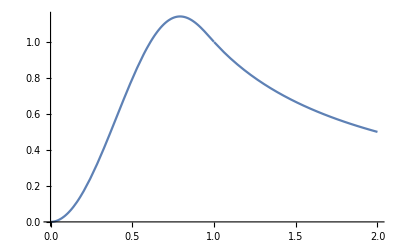

```mathematica
Plot[f[x], {x,0,2}]
```

Equation C2 part 1:

```mathematica
P[r_,theta_]:=P0*f[r]*Sin[theta]^2
```

Poloidal component is defined by the Equation C1:

```mathematica
Bpp =1/r/Sin[theta]* Grad[P[r, theta], {r,theta}, "Polar"] // Simplify
```

{Piecewise[{{-(0.1 Sin[theta])/r^3, r≥1}, {1.125 (0.777778-1.86667 r^2+1. r^4) Sin[theta], True}}],Piecewise[{{(0.2 Cos[theta])/r^3, r≥1}, {0.375 (2.33333-2.8 r^2+1. r^4) Cos[theta], True}}]}

We need to convert it to the Cartesian coordinates:

```mathematica
Bpc=Simplify[TransformedField["Polar"->"Cartesian",Bpp,{r,theta}->{x,y}], x^2+y^2<1]*HeavisideTheta[1-x^2-y^2]
```

{(x y (0.75 x^4-1.05 y^2+0.75 y^4+x^2 (-1.05+1.5 y^2)) HeavisideTheta[1-x^2-y^2])/(x^2+y^2),1/(x^2+y^2)(0.375 x^6+0.875 y^2-2.1 y^4+1.125 y^6+x^4 (-1.05+1.875 y^2)+x^2 (0.875-3.15 y^2+2.625 y^4)) HeavisideTheta[1-x^2-y^2]}

The temporary field looks like:

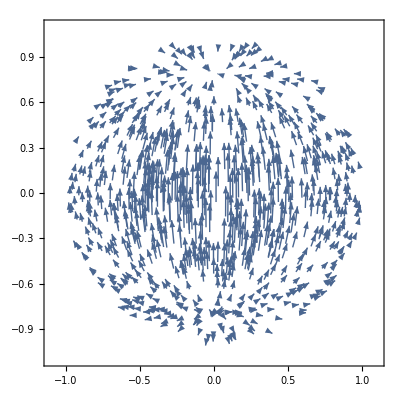

```mathematica
VectorPlot[Bpc,{x,-1,1},{y,-1,1},VectorPoints->RandomReal[{-1,1},{1000,2}]]
```

Finally we need to multiply by unitary vector along phi direction, e_phi, which is equivalent to rotating the vector field by 90 degrees. Here we simply multiply my rotation matrix:

```mathematica
Bpcphi = Bpc.{{0,1},{-1,0}}
```

{-1/(x^2+y^2)(0.375 x^6+0.875 y^2-2.1 y^4+1.125 y^6+x^4 (-1.05+1.875 y^2)+x^2 (0.875-3.15 y^2+2.625 y^4)) HeavisideTheta[1-x^2-y^2],(x y (0.75 x^4-1.05 y^2+0.75 y^4+x^2 (-1.05+1.5 y^2)) HeavisideTheta[1-x^2-y^2])/(x^2+y^2)}

The poloidal component of the field looks like:

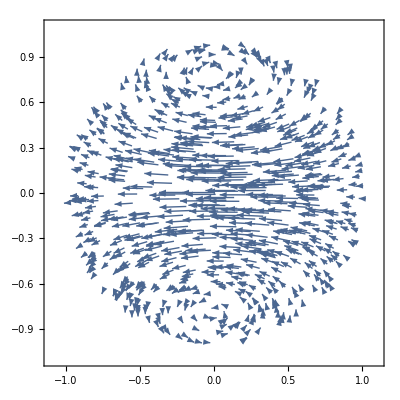

```mathematica
VectorPlot[Bpcphi,{x,-1,1},{y,-1,1},VectorPoints->RandomReal[{-1,1},{1000,2}]]
```

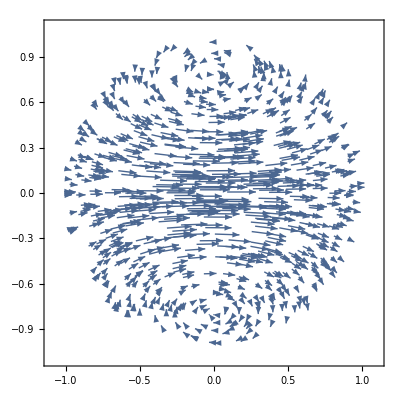

Toroidal component
Eq. C2 part 2

```mathematica
s=100.
```

100.

```mathematica
T[r_,theta_]=s/P0/Rns*(P[r,theta]-P0)^2*HeavisideTheta[P[r,theta]-P0]// Simplify
```

10. HeavisideTheta[-0.1+0.1 (Piecewise[{{1/r, r≥1}, {1/8 r^2 (35-42 r^2+15 r^4), True}}]) Sin[theta]^2] (1.-1. (Piecewise[{{1/r, r≥1}, {1/8 r^2 (35-42 r^2+15 r^4), True}}]) Sin[theta]^2)^2

```mathematica
Btp = 1/r/Sin[theta]*T[r,theta] // Simplify
```

1/r 10. Csc[theta] HeavisideTheta[-0.1+0.1 (Piecewise[{{1/r, r≥1}, {1/8 r^2 (35-42 r^2+15 r^4), True}}]) Sin[theta]^2] (1.-1. (Piecewise[{{1/r, r≥1}, {1/8 r^2 (35-42 r^2+15 r^4), True}}]) Sin[theta]^2)^2

```mathematica
Btc=Simplify[TransformedField["Polar"->"Cartesian",Btp,{r,theta}->{x,y}]](*, x^2+y^2<1]*HeavisideTheta[1-x^2-y^2]*)
```

1/(y (x^2+y^2)^2)10. HeavisideTheta[-0.1+(0.1 y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))/(x^2+y^2)] (1. x^2+1. y^2-1. y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))^2

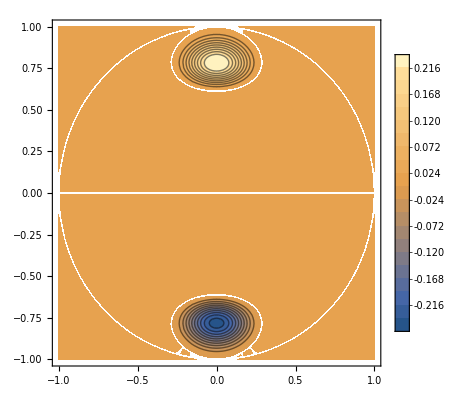

```mathematica
ContourPlot[Btc,{x,-1,1},{y,-1,1},Contours->20,PlotLegends->Automatic]
```

Total magnitude:

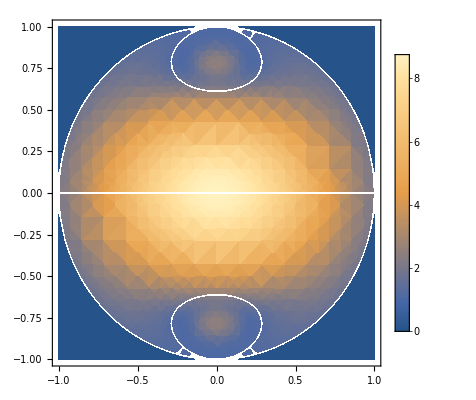

```mathematica
DensityPlot[Sqrt[Btc^2+(Bpcphi.{0,1})^2+(Bpcphi.{1,0})^2],{x,-1,1},{y,-1,1},PlotLegends->Automatic]
```

# Time derivative

Given the magnetic and current fields we can finally write the forces and the time derivative of the magnetic field. For now we assume the current field to be constant.

```mathematica
j3d[x_,y_,z_]={j[x,y].{1,0}, j[x,y].{0,1}, 0}
```

{0.+(y^2 (2.-1.5/(√(x^2+y^2)))+x^2 (1-1/(√(x^2+y^2)))) HeavisideTheta[1-x^2-y^2],-(1. x y (-0.5+1. √(x^2+y^2)) HeavisideTheta[1-x^2-y^2])/(√(x^2+y^2)),0}

```mathematica
B3d[x_,y_,z_] = {Bpcphi.{0,1}, Bpcphi.{1,0},Btc}
```

{(x y (0.75 x^4-1.05 y^2+0.75 y^4+x^2 (-1.05+1.5 y^2)) HeavisideTheta[1-x^2-y^2])/(x^2+y^2),-1/(x^2+y^2)(0.375 x^6+0.875 y^2-2.1 y^4+1.125 y^6+x^4 (-1.05+1.875 y^2)+x^2 (0.875-3.15 y^2+2.625 y^4)) HeavisideTheta[1-x^2-y^2],1/(y (x^2+y^2)^2)10. HeavisideTheta[-0.1+(0.1 y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))/(x^2+y^2)] (1. x^2+1. y^2-1. y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))^2}

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
temp[x_,y_,z_] = CrossProduct[j3d[x,y,z],B3d[x,y,z]]
```

{-1/((x^2+y^2)^(5/2))10. x (-0.5+1. √(x^2+y^2)) HeavisideTheta[1-x^2-y^2] HeavisideTheta[-0.1+(0.1 y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))/(x^2+y^2)] (1. x^2+1. y^2-1. y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))^2,-1/(y (x^2+y^2)^2)10. (0.+(y^2 (2.-1.5/(√(x^2+y^2)))+x^2 (1-1/(√(x^2+y^2)))) HeavisideTheta[1-x^2-y^2]) HeavisideTheta[-0.1+(0.1 y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))/(x^2+y^2)] (1. x^2+1. y^2-1. y^2 (Piecewise[{{1/(√(x^2+y^2)), √(x^2+y^2)≥1}, {1/8 (x^2+y^2) (35-42 (x^2+y^2)+15 (x^2+y^2)^2), True}}]))^2,(1. x^2 y^2 (-0.5+1. √(x^2+y^2)) (0.75 x^4-1.05 y^2+0.75 y^4+x^2 (-1.05+1.5 y^2)) HeavisideTheta[1-x^2-y^2]^2)/((x^2+y^2)^(3/2))-1/(x^2+y^2)(0.375 x^6+0.875 y^2-2.1 y^4+1.125 y^6+x^4 (-1.05+1.875 y^2)+x^2 (0.875-3.15 y^2+2.625 y^4)) HeavisideTheta[1-x^2-y^2] (0.+(y^2 (2.-1.5/(√(x^2+y^2)))+x^2 (1-1/(√(x^2+y^2)))) HeavisideTheta[1-x^2-y^2])}

```mathematica
Simplify[temp, {x=0,y=0.9}]
```

{0.,-0.199149,0.00656}